# atomic emission fiber coupling efficiency

P. Huft

This notebook computes the fraction of light which can be coupled into a single mode fiber, given the light is collected by a lens of a given NA. See the relevant appendix in Young, et. al. “An architecture for quantum networking of neutral atom processors”.

## σ polarization, zero atom temperature

### Field mode definitions

Define the field modes and check that the expressions match Akbar’s, which he wrote in a different form.

```mathematica
Clear["Global`*"]
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ}; (*conj isn't negating all the ⅈ's*)
Eσ= √2 √(3/(16π))(ⅈ ⅇ^(ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),ⅈ};
EσStar=√2 √(3/(16π))(-ⅈ ⅇ^(-ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),-ⅈ};
(*ρ,ϕ; σ+ polarized field mode from radiating dipole*)
EσG=1/(√π w)ⅇ^(-ρ^2/w^2){Cos[ϕ]+ⅈ Sin[ϕ],-(Sin[ϕ]-ⅈ Cos[ϕ])};(*ρ,ϕ; σ+ polarized Gaussian field mode*)
```

```mathematica
Eσ
conj[Eσ]
```

{(ⅈ ⅇ^(ⅈ ϕ) f^(3/2) √(3/π))/(2 (f^2+ρ^2)^(5/4)),-(ⅇ^(ⅈ ϕ) √f √(3/π))/(2 (f^2+ρ^2)^(3/4))}

{(ⅈ ⅇ^(-ⅈ ϕ) f^(3/2) √(3/π))/(2 (f^2+ρ^2)^(5/4)),-(ⅇ^(-ⅈ ϕ) √f √(3/π))/(2 (f^2+ρ^2)^(3/4))}

Check normalization of the field modes

```mathematica
Integrate[ρ EσStar.Eσ,{ρ,0,∞},{ϕ,0,2π},Assumptions->f>0]
```

1

```mathematica
Integrate[ρ conj[EσG].EσG,{ρ,0,∞},{ϕ,0,2π},Assumptions->f>0&&w>0]
```

1

Check that my expressions are the same as Akbar’s

```mathematica
EσStar.EσG//FullSimplify
```

-(ⅈ √(3/2) ⅇ^(-ρ^2/w^2) √f (f+√(f^2+ρ^2)))/(2 π w (f^2+ρ^2)^(5/4))

I verified by hand that the above expression is equivalent to Akbar’s expression below when α=1/(√2),β=ⅈ/(√2), up to an overall factor of 2/w √(2/π), which comes from the normalization factors that Akbar was missing on the field modes (he adds these later).

```mathematica
α=1/(√2);β=ⅈ/(√2);
-ⅇ^(-(ρ/w)^2)(- ⅈ)/(√(ρ^2+f^2))ⅇ^(-ⅈ ϕ)√(3/(16π))√(f/(√(f^2+ρ^2)))(α (1/(√(1+ρ^2/f^2))Cos[ϕ]+ⅈ Sin[ϕ])+β(1/(√(1+ρ^2/f^2))Sin[ϕ]-ⅈ Cos[ϕ]))//FullSimplify
```

(ⅈ ⅇ^(-ρ^2/w^2) √(3/(2 π)) (f/(√(f^2+ρ^2)))^(3/2) (1+√(1+ρ^2/f^2)))/(4 f √(1+ρ^2/f^2))

### Symbolically evaluate overlap integral

Evaluate the indefinite integral over ρ and integrate out ϕ.

```mathematica
Clear[f,w,NA]
(*the indefinite integral*)
overlapIntegralIndef=Integrate[ Integrate[ρ EσStar.EσG,ρ,Assumptions->{f>0,w>0}],{ϕ,0,2π},Assumptions->{f>0,w>0}]
```

(ⅈ √(3/2) ⅇ^(f^2/w^2) √f (f √((f^2+ρ^2)/w^2) Gamma[-1/4,(f^2+ρ^2)/w^2]+√(f^2+ρ^2) Gamma[1/4,(f^2+ρ^2)/w^2]))/(2 w (f^2+ρ^2)^(1/4) ((f^2+ρ^2)/w^2)^(1/4))

```mathematica
Clear[f]
α=1/(√2);β=ⅈ/(√2);
(*Akbar's integral*)
Integrate[Integrate[- ⅈ √(3/(16π))α ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ)
+ √(3/(16π))α ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
-ⅈ √(3/(16π))β ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
- √(3/(16π))β ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ),ρ,Assumptions->{f>0,w0>0}],{ϕ,0,2π},Assumptions->{f>0,w0>0}]
```

(ⅈ ⅇ^(f^2/w0^2) √f √((3 π)/2) (f √((f^2+ρ^2)/w0^2) Gamma[-1/4,(f^2+ρ^2)/w0^2]+√(f^2+ρ^2) Gamma[1/4,(f^2+ρ^2)/w0^2]))/(4 (f^2+ρ^2)^(1/4) ((f^2+ρ^2)/w0^2)^(1/4))

Evaluate the indefinite integral at the desired endpoints to get the definite integral.

```mathematica
overlapIntegral=(overlapIntegralIndef/.ρ->(f NA)/(√(1-NA^2)))-(overlapIntegralIndef/.ρ->0)
```

-(ⅈ √(3/2) ⅇ^(f^2/w^2) √f (f √(f^2/w^2) Gamma[-1/4,f^2/w^2]+√(f^2) Gamma[1/4,f^2/w^2]))/(2 (f^2)^(1/4) (f^2/w^2)^(1/4) w)+(ⅈ √(3/2) ⅇ^(f^2/w^2) √f (f √((f^2+(f^2 NA^2)/(1-NA^2))/w^2) Gamma[-1/4,(f^2+(f^2 NA^2)/(1-NA^2))/w^2]+√(f^2+(f^2 NA^2)/(1-NA^2)) Gamma[1/4,(f^2+(f^2 NA^2)/(1-NA^2))/w^2]))/(2 (f^2+(f^2 NA^2)/(1-NA^2))^(1/4) ((f^2+(f^2 NA^2)/(1-NA^2))/w^2)^(1/4) w)

General::munfl: Exp[-1119.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1116.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1119.88] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

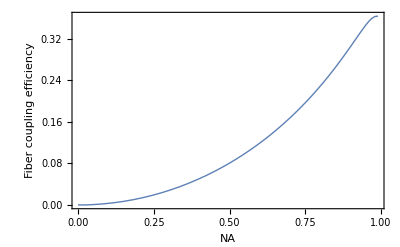

```mathematica
Clear[w,NA];
NAList=Range[0,0.99,0.01];
f=6*^-3;
wTable=Range[100]/100 3f;(*the range Akbar used*)
couplingEfficiencyList={};
wBestList={};
For[i=1,i<Length[NAList]+1,i++,
NA=NAList[[i]];
integralResult=Select[Array[1/2 Abs[overlapIntegral/.w->wTable[[#]]]^2&,Length[wTable]],#<100&];
{res,wBest}=SortBy[Transpose@{integralResult,wTable},#1&][[-1]];
AppendTo[couplingEfficiencyList,res];
AppendTo[wBestList,wBest];
]
ListPlot[Transpose@{NAList,couplingEfficiencyList},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Fiber coupling efficiency"}]
```

### Numerically evaluate overlap integral

The result below agrees with the symbolic result

```mathematica
Clear[w,NA];
NAList=Range[0,0.99,0.01];
f=6*^-3;
wTable=Range[100]/100 3f;(*the range Akbar used*)
couplingEfficiencyList={};
wBestList={};
For[i=1,i<Length[NAList]+1,i++,
NA=NAList[[i]];
ρNA=(f NA)/(√(1-NA^2));
integralResult=Select[Array[1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wTable[[#]],{ρ,0,ρNA},{ϕ,0,2π}]]^2&,Length[wTable]],#<100&];
{res,wBest}=SortBy[Transpose@{integralResult,wTable},#1&][[-1]];
AppendTo[couplingEfficiencyList,res];
AppendTo[wBestList,wBest];
]
```

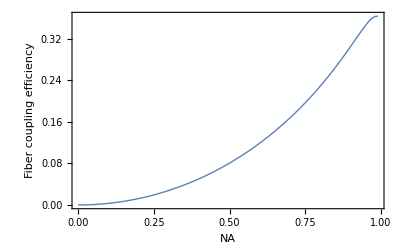

```mathematica
ListPlot[Transpose@{NAList,couplingEfficiencyList},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Fiber coupling efficiency"}]
```

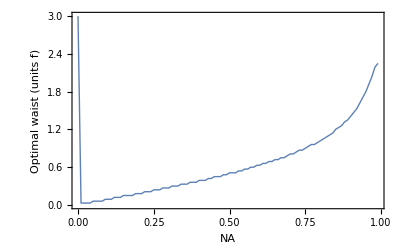

```mathematica
ListPlot[Transpose@{NAList,wBestList/f},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Optimal waist (units f)"}]
```

Now, how does the fiber coupling efficiency depend on the waist we are matching to, for a given focal length and NA?

```mathematica
(*the network node parabolic mirror parameters*)
f=5.26*^-3;
NA=0.61;

couplingEfficiencyList={};
wTable=Range[1*^-3,6*^-3,1*^-4];
ρNA=(f NA)/(√(1-NA^2));
integralResult=Array[1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wTable[[#]],{ρ,0,ρNA},{ϕ,0,2π}]]^2&,Length[wTable]];
```

```mathematica
ListPlot[Transpose@{wTable*1*^3,integralResult},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"Collimated mode waist (mm)","Fiber coupling efficiency"}]
```

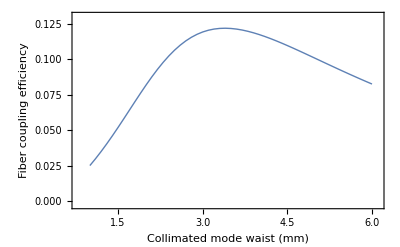

What is the theoretical coupling efficiency for our network node?

```mathematica
wFiber=2.4*^-6;(*Fibercore SM800 fiber*)
fLens=30*^-3;(*Edmund 9mm Dia.x 30mm FL,NIR II Coated,Achromatic Lens*)
"collimated mode waist from fiber"
wMode=(fLens 7.8*^-7)/(π wFiber)
```

collimated mode waist from fiber

0.00310352

```mathematica
"theoretical best fiber coupling efficiency in parabolic mirror node"
1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wMode,{ρ,0.25*^-3,ρNA},{ϕ,0,2π}]]^2(*note that I start the ρ integration at 0.25mm,because of the hole in the mirror*)
```

theoretical best fiber coupling efficiency in parabolic mirror node

0.120038

How much does the axial hole effect the efficiency?

```mathematica
1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wMode,{ρ,0,ρNA},{ϕ,0,2π}]]^2-1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wMode,{ρ,0.25*^-3,ρNA},{ϕ,0,2π}]]^2
```

0.0022984

### collection efficiency plot evaluated using the lens transform

```mathematica
Clear[f,k]
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k r+ϕ)))/r{Cos[θ],ⅈ};(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k r+ϕ)))/r{Cos[θ],-ⅈ};
EσAfterLens=(EσBeforeLens √Cos[θ])/.{r->√(ρ^2+f^2),Cos[θ]->f/(√(f^2+ρ^2))};(*ρ,ϕ*)
EσAfterLensStar=EσBeforeLensStar √Cos[θ]/.{r->√(ρ^2+f^2),Cos[θ]->f/(√(f^2+ρ^2))};
EσG=1/(√π w)ⅇ^(-ρ^2/w^2){Cos[ϕ]+ⅈ Sin[ϕ],-(Sin[ϕ]-ⅈ Cos[ϕ])};(*ρ,ϕ; σ+ polarized Gaussian field mode*)
λ=0.78*^-7;
k=λ/(2π);
```

```mathematica
Clear[w,NA];
NAList=Range[0,0.99,0.01];
f=6*^-3;
wTable=Range[100]/100 3f;(*the range Akbar used*)
couplingEfficiencyList={};
wBestList={};
For[i=1,i<Length[NAList]+1,i++,
NA=NAList[[i]];
ρNA=(f NA)/(√(1-NA^2));
integralResult=Select[Array[1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.w->wTable[[#]],{ρ,0,ρNA},{ϕ,0,2π}]]^2&,Length[wTable]],#<100&];
{res,wBest}=SortBy[Transpose@{integralResult,wTable},#1&][[-1]];
AppendTo[couplingEfficiencyList,res];
AppendTo[wBestList,wBest];
]
```

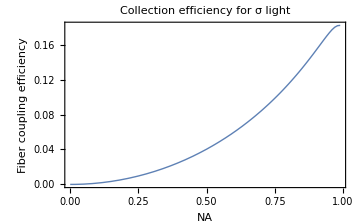

```mathematica
ListPlot[Transpose@{NAList,couplingEfficiencyList},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Fiber coupling efficiency"},PlotLabel->"Collection efficiency for σ light"]
```

### bonus: estimate our dipole trap depth

This is kind of stupid, but if we assume our collection optics are well aligned, and we know the quantum efficiency of our detector and other losses, we can estimate the detuning of our light from the atom given an estimate of our Rabi frequency, and consequently back out the trap depth since we know how many photons we scatter per s and what the detuning is compared to the bare atomic states. todo...

## σ polarization, finite atom temperature

### Verify that the overlap integral can be taken in any transverse plane after the lens

```mathematica
Clear["Global`*"];
(*displace the atom from lens focus location*)
x0=0;
y0=0;
z0=0;
f=5.26*^-3;
NA=0.61;
λ=7.8*^-7;
k=2π /λ;
rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];
EσAfterLensStar=((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};
EσG=1/(√π w)ⅇ^(-ρ^2/w^2){Cos[ϕ]+ⅈ Sin[ϕ],-(Sin[ϕ]-ⅈ Cos[ϕ]),0};(*ρ,ϕ,z basis; σ+ polarized Gaussian field mode*)
wMode=0.63 f;(*doesn't really matter for this test, but this is close to optimal*)

(*now evaluate the integral in a few different transverse planes*)
ρNA=(f NA)/(√(1-NA^2));
"overlap integral result plane 0"
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"GlobalAdaptive"]]^2
(*"overlap integral result plane 1"
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0.001},{ρ,0,ρNA},{ϕ,0,2π}]]^2
"overlap integral result plane 2"
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0.01},{ρ,0,ρNA},{ϕ,0,2π}]]^2*)
```

overlap integral result plane 0

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"GlobalAdaptive"]]^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"LocalAdaptive"]]^2
```

$Aborted

```mathematica
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"DoubleExponential"]]^2
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϕ in the region {{0,0.00375},{0,6.283185307}}. NIntegrate obtained -6.85358136456241895628990519008846303414248993467005116654037×10^-8+1.08152663986871967957305023113570392754165730466812145003154×10^-7 ⅈ and 0.00632382625309900061479330470784842011164422973672322584693552 for the integral and error estimates.

8.19707824×10^-15

```mathematica
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"Trapezoidal"]]^2
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϕ in the region {{0,0.00375},{0,6.283185307}}. NIntegrate obtained 4.935025703×10^-14+2.434052449×10^-14 ⅈ and 9.064510399×10^-14 for the integral and error estimates.

1.5139545×10^-27

```mathematica
1/2 Abs[NIntegrate[ρ EσAfterLensStar.EσG/.{w->wMode,z->0},{ρ,0,ρNA},{ϕ,0,2π},WorkingPrecision->10,Method->"Trapezoidal"]]^2
```

The integral is either not converging or giving a very small value even when I expect the result to be ~ 0.1 or so. Check that the integrands-- the original version above for an atom at the lens focus, and the one for an atom at a general location-- evaluated give the same value when evaluated at the origin

```mathematica
x0=y0=z0=0;
EσStar=√2 √(3/(16π))(-ⅈ ⅇ^(-ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),-ⅈ,0};(*ρ,ϕ,z basis;the original expression for the field after the lens from the sigma emission*)
EσStar.EσG/.{ρ->0.0001,ϕ->0.1,w->wMode}
EσAfterLensStar.EσG/.{ρ->0.0001,ϕ->0.1,w->wMode,z->0}
```

0.-22337.3 ⅈ

15237.7-4158.07 ⅈ

```mathematica
(*this still gives the correct result*)
1/2 Abs[NIntegrate[ρ EσStar.EσG/.{w->wMode},{ρ,0,ρNA},{ϕ,0,2π}]]^2
```

0.123644

Set different variables to 0 to isolate which ones are involved in the error.

```mathematica
EσStar.EσG/.{ρ->0,ϕ->0.1,w->wMode}
EσAfterLensStar.EσG/.{ρ->0,ϕ->0.1,w->wMode,z->0}
```

-2.27374×10^-13-22365.8 ⅈ

7075.9+14143.7 ⅈ

```mathematica
EσStar.EσG/.{ρ->0.001,ϕ->0,w->wMode}
EσAfterLensStar.EσG/.{ρ->0.001,ϕ->0,w->wMode,z->0}
```

0.-19707.5 ⅈ

-9790.52+9916.61 ⅈ

```mathematica
EσStar.EσG/.{ρ->0,ϕ->0,w->wMode}
EσAfterLensStar.EσG/.{ρ->0,ϕ->0,w->wMode,z->0}
```

0.-22365.8 ⅈ

8452.57+13366.7 ⅈ

The two expressions disagree even for ρ and ϕ set to zero.

### Numerically evaluate overlap integral

For finite atom temperature, the emitter is no longer guaranteed to be at the focus of the collection lens. Considering a single atom in a harmonic trap of a given depth, where the lifetime of the relevant transition is much shorter than the frequency of motion in the trap, we can average over the atomic positions to find the average efficiency for emitted light coupled into a fiber (again, we will assume σ polarized light).

Todo: use my result for the transformed field from a displaced atom (the see grid visualization cell)

```mathematica
(*I pasted the wBestList result from the zero temperature result for each NA step*)
NAList=Range[0,0.99,0.01];
wBestList={9/500,9/50000,9/50000,9/50000,9/50000,9/25000,9/25000,9/25000,9/25000,27/50000,27/50000,27/50000,9/12500,9/12500,9/12500,9/10000,9/10000,9/10000,9/10000,27/25000,27/25000,27/25000,63/50000,63/50000,63/50000,9/6250,9/6250,9/6250,81/50000,81/50000,81/50000,9/5000,9/5000,9/5000,99/50000,99/50000,99/50000,27/12500,27/12500,27/12500,117/50000,117/50000,117/50000,63/25000,63/25000,27/10000,27/10000,27/10000,9/3125,9/3125,153/50000,153/50000,153/50000,81/25000,81/25000,171/50000,171/50000,9/2500,9/2500,189/50000,189/50000,99/25000,99/25000,207/50000,207/50000,27/6250,27/6250,9/2000,9/2000,117/25000,243/50000,243/50000,63/12500,261/50000,261/50000,27/5000,279/50000,18/3125,18/3125,297/50000,153/25000,63/10000,81/12500,333/50000,171/25000,9/1250,369/50000,189/25000,99/12500,81/10000,423/50000,441/50000,459/50000,243/25000,513/50000,27/2500,36/3125,153/12500,657/50000,27/2000};
```

```mathematica
wBestList[[60]]/f
```

63/100

```mathematica
Clear[w,NA];
MonteCarloSteps=10;
TFORT=1*^-3;(*K*)
Tatom=1*^-5;(*K*)
w0=0.7*^-6;
λ=0.852*^-6;
zR=π w0^2/λ;
σρ=w0/(√2)√(Tatom/TFORT);
σz=zR/(√2)√(Tatom/TFORT);
NAList=Range[0,0.99,0.05];
f=6*^-3;
wTable=Range[100]/100 3f;(*the range Akbar used*)
couplingEfficiencyList={};
wBestList={};
For[i=1,i<Length[NAList]+1,i++,
NA=NAList[[i]];
ρNA=(f NA)/(√(1-NA^2));
For[j=1,j<=MonteCarloSteps,j++,
integralResult=Select[Array[1/2 Abs[NIntegrate[ρ EσStar.EσG/.w->wTable[[#]],{ρ,0,ρNA},{ϕ,0,2π}]]^2&,Length[wTable]],#<100&];
{res,wBest}=SortBy[Transpose@{integralResult,wTable},#1&][[-1]];
AppendTo[couplingEfficiencyList,res];
AppendTo[wBestList,wBest];
]
```

```mathematica
ListPlot[Transpose@{NAList,couplingEfficiencyList},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Fiber coupling efficiency"}]
```

-Graphics-

```mathematica
ListPlot[Transpose@{NAList,wBestList/f},Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA","Optimal waist (units f)"}]
```

-Graphics-

## misc testing

### emission pattern before and after lens (correct)

```mathematica
Clear[f]
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k r+ϕ)))/r{Cos[θ],ⅈ};(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k r+ϕ)))/r{Cos[θ],-ⅈ};
"intensity pattern before lens (spherical coords.)"
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar

EσAfterLens=√(3/(16π))(ⅈ ⅇ^(ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),ⅈ};(*ρ,ϕ*)
EσAfterLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),-ⅈ};
"intensity pattern after lens (cylindrical coords.)"
intensityAfterLens=EσAfterLens.EσAfterLensStar
f=5*^-3;
λ=0.78*^-6;
k=(2π)/λ;
```

intensity pattern before lens (spherical coords.)

3/(16 π r^2)+(3 Cos[θ]^2)/(16 π r^2)

intensity pattern after lens (cylindrical coords.)

(3 f^3)/(16 π (f^2+ρ^2)^(5/2))+(3 f)/(16 π (f^2+ρ^2)^(3/2))

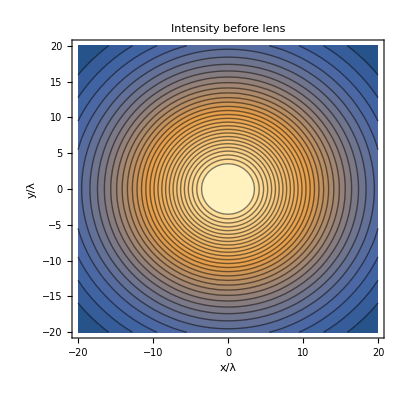

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x λ)^2+(y λ)^2+0.000000000001),θ->π/2},{x,-20,20},{y,-20,20},Contours->30,FrameLabel->{"x/λ","y/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

```mathematica
(√(.0000000001))/λ
```

12.8205

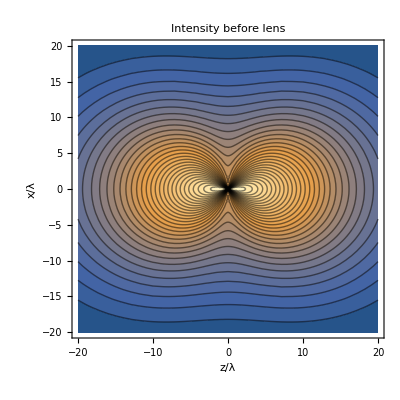

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x λ)^2+(z λ)^2+.0000000001),θ->ArcTan[z,x]},{z,-20,20},{x,-20,20},Contours->30,FrameLabel->{"z/λ","x/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

```mathematica
√(.0000000001)
```

0.00001

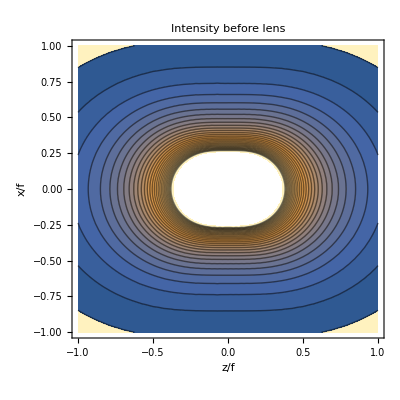

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x f)^2+(z f)^2+0.000000000001),θ->ArcTan[x/z]},{z,-1,1},{x,-1,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

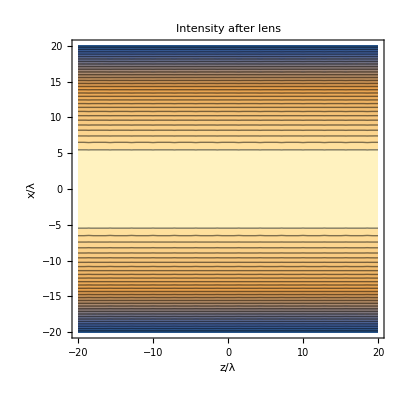

```mathematica
ContourPlot[intensityAfterLens/.{ρ->√((x λ)^2+0.000000000001)},{z,-20,20},{x,-20,20},Contours->30,FrameLabel->{"z/λ","x/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity after lens"]
```

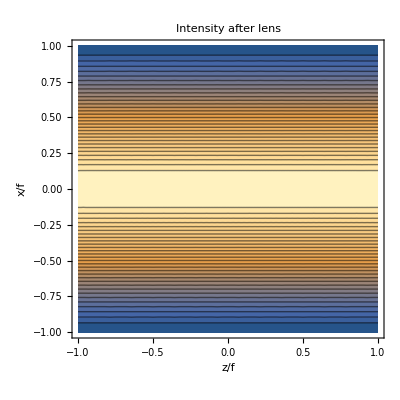

```mathematica
ContourPlot[intensityAfterLens/.{ρ->√((x f)^2+0.000000000001)},{z,-1,1},{x,-1,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity after lens"]
```

### emission pattern before and after lens, no coordinate offset - use the lens transform (correct)

this cell gets the field after the lens using the appropriate coordinate mappings

```mathematica
Clear[f,k]
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k r+ϕ)))/r{Cos[θ],ⅈ};(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k r+ϕ)))/r{Cos[θ],-ⅈ};
"intensity pattern before lens (spherical coords.)"
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar

EσAfterLens=(EσBeforeLens √Cos[θ])/.{r->√(ρ^2+f^2),Cos[θ]->f/(√(f^2+ρ^2))};(*ρ,ϕ*)
EσAfterLensStar=EσBeforeLensStar √Cos[θ]/.{r->√(ρ^2+f^2),Cos[θ]->f/(√(f^2+ρ^2))};
"intensity pattern after lens (cylindrical coords.)"
intensityAfterLens=EσAfterLens.EσAfterLensStar
f=5*^-3;
λ=0.78*^-7;
k=λ/(2π);
```

intensity pattern before lens (spherical coords.)

3/(16 π r^2)+(3 Cos[θ]^2)/(16 π r^2)

intensity pattern after lens (cylindrical coords.)

(3 f^3)/(16 π (f^2+ρ^2)^(5/2))+(3 f)/(16 π (f^2+ρ^2)^(3/2))

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x λ)^2+(y λ)^2+0.000000000001),θ->π/2},{x,-20,20},{y,-20,20},Contours->30,FrameLabel->{"x/λ","y/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

-Graphics-

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x λ)^2+(z λ)^2+0.000000000001),θ->ArcTan[x/z]},{z,-20,20},{x,-20,20},Contours->30,FrameLabel->{"z/λ","x/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

-Graphics-

```mathematica
ContourPlot[intensityBeforeLens/.{r->√((x f)^2+(z f)^2+0.000000000001),θ->ArcTan[x/z]},{z,-1,1},{x,-1,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity before lens"]
```

-Graphics-

```mathematica
ContourPlot[intensityAfterLens/.{ρ->√((x λ)^2+0.000000000001)},{z,-20,20},{x,-20,20},Contours->30,FrameLabel->{"z/λ","x/λ"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity after lens"]
```

-Graphics-

```mathematica
ContourPlot[intensityAfterLens/.{ρ->√((x f)^2+0.000000000001)},{z,-1,1},{x,-1,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->14],PlotLabel->"Intensity after lens"]
```

-Graphics-

### spherical coordinates origin shift (r vector and unit vectors - correct)

```mathematica
Clear["Global`*"]
```

```mathematica
rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[rr Cos[ϕ]Sin[θ]-x0,rr Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/rr];
$Assumptions={r>0,θ∈Reals}
```

{r>0,θ∈ℝ}

```mathematica
θθ/.{x0->0,y0->0,z0->0}//FullSimplify
```

ArcCos[Cos[θ]]

```mathematica
ϕϕ/.{x0->0,y0->0,z0->0}//FullSimplify
```

```mathematica
ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]
```

```mathematica
rr/.{x0->0,y0->0,z0->0}//FullSimplify
```

r

What I’ve solved below is inverse of what I actually want to do, which is to say that I have defined the coordinates in the unprimed space in terms of the primed ones (double letters), whereas I want to express the primed coordinates in terms of the unprimed since I want to integrate something in the primed frame over the unprimed frame coordinates.

```mathematica
Clear["Global`*"]
rr=1;
ϕϕ=π/3;
θθ=π/4;
r=√((x0+rr Cos[ϕϕ]Sin[θθ])^2+(y0+rr Sin[ϕϕ]Sin[θθ])^2+(z0+rr Cos[θθ])^2);
θ=ArcCos[(rr Cos[θθ]+z0)/r];
ϕ=ArcTan[x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ]];
x0=1;
y0=0.1;
z0=0.1;
arrowPrime=Arrow[{{x0,y0,z0},{x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ],z0+rr Cos[θθ]}}];
arrow =Arrow[{{0,0,0},{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]}}];
Graphics3D[{Red,arrow,Blue,arrowPrime},Axes->True,PlotRange->{{-2,2},{-2,2},{-2,2}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Below, the primed frame coordinates are expressed in terms of the unprimed ones, which is what is needed for mapping the dipole radiation with the lens transform.

```mathematica
Clear["Global`*"]
r=1;
ϕ=π/6;
θ=π/5;
rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ]Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
θθ=ArcCos[(r Cos[θ]-z0)/rr];
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
x0=1;
y0=0.1;
z0=0.1;
arrowPrime=Arrow[{{x0,y0,z0},{x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ],z0+rr Cos[θθ]}}];
arrow =Arrow[{{0,0,0},{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]}}];
Graphics3D[{Red,arrow,Blue,arrowPrime},Axes->True,PlotRange->{{-2,2},{-2,2},{-2,2}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Now include the unit vectors  for both coordinate systems and a spiffy manipulator.

```mathematica
Clear["Global`*"]
r=2;
rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ]Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
θθ=ArcCos[(r Cos[θ]-z0)/rr];
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
x0=1;
y0=0.1;
z0=0.1;
arrowPrime=Arrow[{{x0,y0,z0},{x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ],z0+rr Cos[θθ]}}];(*points to the coordinate (rr,θθ,ϕϕ)*)
ϕHatPrime=Arrow[{{x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ],z0+rr Cos[θθ]},{x0+rr Cos[ϕϕ]Sin[θθ]-Sin[ϕϕ],y0+rr Sin[ϕϕ]Sin[θθ]+Cos[ϕϕ],z0+rr Cos[θθ]}}];
θHatPrime=Arrow[{{x0+rr Cos[ϕϕ]Sin[θθ],y0+rr Sin[ϕϕ]Sin[θθ],z0+rr Cos[θθ]},{x0+rr Cos[ϕϕ]Sin[θθ]-Cos[ϕϕ]Cos[θθ],y0+rr Sin[ϕϕ]Sin[θθ]-Sin[ϕϕ]Cos[θθ],z0+rr Cos[θθ]+Sin[θθ]}}];
arrow =Arrow[{{0,0,0},{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]}}];(*points to the coordinate (r,θ,ϕ)*)
θHat=Arrow[{{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]},{r Cos[ϕ]Sin[θ]-Cos[ϕ]Cos[θ],r Sin[ϕ]Sin[θ]-Sin[ϕ]Cos[θ],r Cos[θ]+Sin[θ]}}];
α =-Cos[θ-θθ]Cos[ϕ];
θHatPrimeθHatComponent=Arrow[{{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]},{r Cos[ϕ]Sin[θ]-α Cos[ϕ]Cos[θ],r Sin[ϕ]Sin[θ]-α Sin[ϕ]Cos[θ],r Cos[θ]+α Sin[θ]}}];
ϕHat=Arrow[{{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]},{r Cos[ϕ]Sin[θ]-Sin[ϕ],r Sin[ϕ]Sin[θ]+Cos[ϕ],r Cos[θ]}}];
styles={Red,Directive[Red,Dashing[0.005]],Directive[Red,Dashing[0.02]],Blue,Directive[Blue,Dashing[0.005]],Directive[Blue,Dashing[0.02]],Orange};
objects ={arrow,ϕHat,θHat,arrowPrime,ϕHatPrime,θHatPrime,θHatPrimeθHatComponent};
labels={"r̂","ϕ̂","θ̂","r̂'","ϕ̂'","θ̂'","(θ̂'.θ̂)θ̂"};
Manipulate[Evaluate[Legended[Graphics3D[Transpose@{styles,objects},Axes->True,PlotRange->{{-1.5r,1.5r},{-1.5r,1.5r},{-1.5r,1.5r}},AxesLabel->{"x","y","z"}],LineLegend[styles,labels]]],{ϕ,10^-6,2π-10^-6},{θ,10^-6,π-10^-6}]
```

Rename and redefine the graphics in terms of defined vectors.

```mathematica
Clear["Global`*"]
r=2;
rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ]Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
θθ=ArcCos[(r Cos[θ]-z0)/rr];
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
x0=1;
y0=0.1;
z0=0.1;
originPrime={x0,y0,z0};
origin={0,0,0};
rVecPrime={rr Cos[ϕϕ]Sin[θθ],rr Sin[ϕϕ]Sin[θθ],rr Cos[θθ]}+originPrime;
rVecPrimeArrow=Arrow[{originPrime,rVecPrime}];(*points to the coordinates (rr,θθ,ϕϕ)*)
ϕHatPrime={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHatPrimeArrow=Arrow[{rVecPrime,ϕHatPrime+rVecPrime}];
θHatPrime={-Cos[ϕϕ]Cos[θθ],-Sin[ϕϕ]Cos[θθ],Sin[θθ]};
θHatPrimeArrow=Arrow[{rVecPrime,θHatPrime+rVecPrime}];
rVecArrow=Arrow[{origin,{r Cos[ϕ]Sin[θ],r Sin[ϕ]Sin[θ],r Cos[θ]}}];(*points to the coordinates (r,θ,ϕ)*)
θHat={-Cos[ϕ]Cos[θ],-Sin[ϕ]Cos[θ],Sin[θ]};
θHatArrow=Arrow[{rVecPrime,θHat+rVecPrime}];
θHatPrimeθHatComponentArrow=Arrow[{rVecPrime,(θHatPrime.θHat)θHat+rVecPrime}];
ϕHat={-Sin[ϕ],Cos[ϕ],0};
ϕHatArrow=Arrow[{rVecPrime,ϕHat+rVecPrime}];
styles={Red,Directive[Red,Dashing[0.005]],Directive[Red,Dashing[0.02]],Blue,Directive[Blue,Dashing[0.005]],Directive[Blue,Dashing[0.02]],Orange};
objects ={rVecArrow,ϕHatArrow,θHatArrow,rVecPrimeArrow,ϕHatPrimeArrow,θHatPrimeArrow,θHatPrimeθHatComponentArrow};
labels={"r̂","ϕ̂","θ̂","r̂'","ϕ̂'","θ̂'","(θ̂'.θ̂)θ̂"};
Manipulate[Evaluate[Legended[Graphics3D[Transpose@{styles,objects},Axes->True,PlotRange->{{-1.5r,1.5r},{-1.5r,1.5r},{-1.5r,1.5r}},AxesLabel->{"x","y","z"}],LineLegend[styles,labels]]],{ϕ,10^-6,2π-10^-6},{θ,10^-6,π-10^-6}]
```

### spherical polar plots to test coordinate shift (correct, but in polar coordinates)

```mathematica
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-



```mathematica
PolarPlot[1,{θ,0,2π}]
```

```mathematica
Clear["Global`"]
rr=1;
Manipulate[PolarPlot[(2x0 Cos[θ]+√(4 x0^2 Cos[θ]^2-4(x0^2-rr^2)))/2,{θ,0,2π},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{x0,10^-6,0.5}]
```

```mathematica
Manipulate[PolarPlot[x0 Cos[θ]+y0 Sin[θ]+√((x0 Cos[θ]+y0 Sin[θ])^2-(x0^2+y0^2-rr^2)),{θ,0,2π},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{x0,-0.5,0.5},{y0,-0.5,0.5}]
```

```mathematica
Manipulate[SphericalPlot3D[x0 Cos[ϕ]Sin[θ]+y0 Sin[ϕ]Sin[θ]+z0 Cos[θ]+√((x0 Cos[ϕ]Sin[θ]+y0 Sin[ϕ]Sin[θ]+z0 Cos[θ])^2-(x0^2+y0^2+z0^2-rr^2)),{θ,0,π},{ϕ,0,2π},PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}],{x0,-0.5,0.5},{y0,-0.5,0.5},{z0,-0.5,0.5}]
```

### Spherical coordinates offset (attempt 4 - correct)

I think the radial coordinate may have been the main offender. In any case, here I try to heuristically arrive at the correct result by gradually replacing Cartesian coordinates with their spherical equivalents, and adding in angular dependence to the test function later.

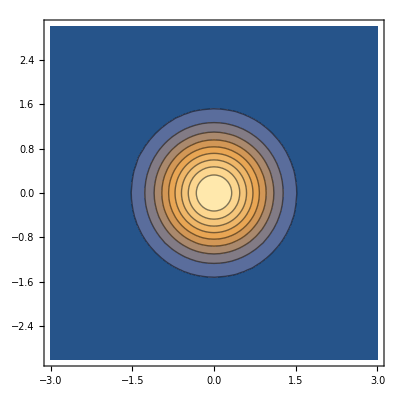

```mathematica
ContourPlot[Exp[-r^2]/.r->√(x^2+y^2),{x,-3,3},{y,-3,3},PlotRange->All]
```

```mathematica
Manipulate[ContourPlot[Exp[-((r Cos[θ]-x0)^2+(r Sin[θ]-y0)^2)]/.{r->√(x^2+y^2),θ->ArcTan[x,y]},{x,-3,3},{y,-3,3},PlotRange->All],{x0,-0.5,0.5},{y0,-0.5,0.5}]
```

Move up to a function in three dimensions.

```mathematica
z=0;
Manipulate[ContourPlot[Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+y^2+z^2),ϕ->ArcTan[x,y],θ->ArcCos[z/(√(x^2+y^2+z^2))]},{x,-3,3},{y,-3,3},PlotLegends->Automatic,PlotRange->{0,1}],{x0,-0.5,0.5},{y0,-0.5,0.5},{z0,-0.5,0.5}]
```

Now, add in angular dependence. We want the angular dependence to remain fixed with respect to the coordinate system whose origin is (x0,y0,z0).

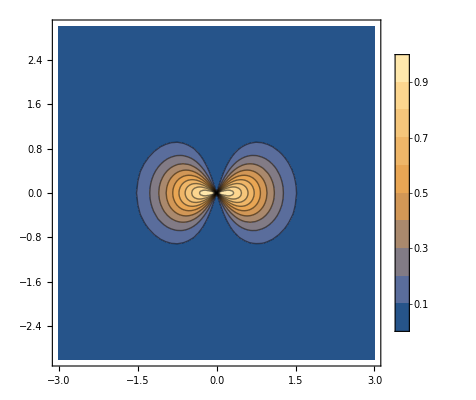

```mathematica
z=0;
ContourPlot[(1+Cos[2ϕ])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+y^2+z^2),ϕ->ArcTan[x,y],θ->ArcCos[z/(√(x^2+y^2+z^2))],x0->0,y0->0,z0->0},{x,-3,3},{y,-3,3},PlotLegends->Automatic,PlotRange->{0,1}]
```

Add in a second plot and make sure the translations are occurring in the correct directions before correcting the angular dependence for finite coordinate displacement.

```mathematica
Clear["Global`"]
Manipulate[Grid[{{ContourPlot[(1+Cos[2ϕ])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+y^2+z^2),ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{x,-3,3},{y,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","y"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[(1+Cos[2ϕ])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+0+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√(x^2+0+z^2))]},{x,-3,3},{z,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","z"},LabelStyle->Directive[Black, FontSize->12]]}}],{x0,-0.5,0.5},{y0,-0.5,0.5},{z0,-0.5,0.5}]
```

Now correct the angular dependence.

```mathematica
Clear["Global`"]
(*r'=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)*)
(*ϕ'=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]*)
Manipulate[Grid[{{ContourPlot[(1+Cos[2ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+y^2+z^2),ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{x,-3,3},{y,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","y"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[(1+Cos[2ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+0+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√(x^2+0+z^2))]},{x,-3,3},{z,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","z"},LabelStyle->Directive[Black, FontSize->12]]}}],{x0,-0.5,0.5},{y0,-0.5,0.5},{z0,-0.5,0.5}]
```

Finally, make the function dependent on θ as well, so we have dependence on all three spherical coordinates (I added an overall factor of (Sin(θ'/2))^2 )

```mathematica
Clear["Global`"]
(*r'=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)*)
(*θ'=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]*)
(*ϕ'=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]*)
Manipulate[Grid[{{ContourPlot[Sin[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]/2]^2(1+Cos[2ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+y^2+z^2),ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{x,-3,3},{y,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","y"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[Sin[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]/2]^2(1+Cos[2ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]])/2 Exp[-((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)]/.{r->√(x^2+0+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√(x^2+0+z^2))]},{x,-3,3},{z,-3,3},PlotLegends->Automatic,PlotRange->{0,1},FrameLabel->{"x","z"},LabelStyle->Directive[Black, FontSize->12]]}}],{x0,-0.5,0.5},{y0,-0.5,0.5},{z0,-0.5,0.5}]
```

### Emission pattern before lens with coordinate offset (correct)

This takes into account how the primed coordinates change in terms of the unprimed coordinates and the origin location, but the components are only θ and ϕ still. If we are only considering intensity, this may work out okay, but is incomplete.

```mathematica
Clear["Global`"]
(*r'=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)*)
(*θ'=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]*)
(*ϕ'=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]*)
λ=7.8*^-7;
k=2π /λ;
fmax=1;(*max contour plot value*)
xmax=10;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k √((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)+ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0])))/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)){Cos[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]],ⅈ };(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k √((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)+ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0])))/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)){Cos[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]],-ⅈ };
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar
zoffset=0.00001;
yoffset=0;
Manipulate[Grid[{{ContourPlot[(3 (-z0+r Cos[θ])^2)/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2))/.{r->√((x λ)^2+(y λ)^2+0),ϕ->ArcTan[x,y],θ->ArcCos[0/(√((x λ)^2+(y λ)^2+0))]},{x,-xmax,xmax},{y,-xmax,xmax},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"x","y"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[(3 (-z0+r Cos[θ])^2)/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2))/.{r->√((x λ)^2+(yoffset λ)^2+(z λ)^2),ϕ->ArcTan[x λ,yoffset λ],θ->ArcCos[(z λ)/(√((x λ)^2+(yoffset λ)^2+(z λ)^2))]},{x,-xmax,xmax},{z,-xmax,xmax},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"x","z"},LabelStyle->Directive[Black, FontSize->12]]}}],{{x0,0},-10 λ,10 λ},{{y0,0},-10 λ,10 λ},{{z0,0},-10 λ,10 λ}]
```

(3 (-3.9×10^-7+r Cos[θ])^2)/(16 π ((-3.9×10^-7+r Cos[θ])^2+(0.+r Cos[ϕ] Sin[θ])^2+(-3.9×10^-7+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-3.9×10^-7+r Cos[θ])^2+(0.+r Cos[ϕ] Sin[θ])^2+(-3.9×10^-7+r Sin[θ] Sin[ϕ])^2))

ContourPlot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

```mathematica
Clear["Global`"]
(*r'=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)*)
(*θ'=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]*)
(*ϕ'=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0]*)
λ=7.8*^-7;
k=2π /λ;
fmax=1;(*max contour plot value*)
xmax=10;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k √((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)+ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0])))/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)){Cos[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]],ⅈ };(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k √((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)+ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0])))/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2)){Cos[ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))]],-ⅈ };
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar
zoffset=0.00001;
yoffset=0;
Manipulate[Grid[{{ContourPlot[(3 (-z0+r Cos[θ])^2)/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2))/.{r->√((x λ)^2+(y λ)^2+0),ϕ->ArcTan[x,y],θ->ArcCos[0/(√((x λ)^2+(y λ)^2+0))]},{x,-xmax,xmax},{y,-xmax,xmax},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"x","y"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[(3 (-z0+r Cos[θ])^2)/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-z0+r Cos[θ])^2+(-x0+r Cos[ϕ] Sin[θ])^2+(-y0+r Sin[θ] Sin[ϕ])^2))/.{r->√((x λ)^2+(yoffset λ)^2+(z λ)^2),ϕ->ArcTan[x λ,yoffset λ],θ->ArcCos[(z λ)/(√((x λ)^2+(yoffset λ)^2+(z λ)^2))]},{x,-xmax,xmax},{z,-xmax,xmax},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"x","z"},LabelStyle->Directive[Black, FontSize->12]]}}],{{x0,0},-10 λ,10 λ},{{y0,0},-10 λ,10 λ},{{z0,0},-10 λ,10 λ}]
```

(3 (-3.9×10^-7+r Cos[θ])^2)/(16 π ((-3.9×10^-7+r Cos[θ])^2+(0.+r Cos[ϕ] Sin[θ])^2+(-3.9×10^-7+r Sin[θ] Sin[ϕ])^2)^2)+3/(16 π ((-3.9×10^-7+r Cos[θ])^2+(0.+r Cos[ϕ] Sin[θ])^2+(-3.9×10^-7+r Sin[θ] Sin[ϕ])^2))

ContourPlot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

### Intensity pattern after the lens transformation (looks correct)

```mathematica
Clear["Global`*"]
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=10f/λ; (*plot half width value, units λ*)
xmaxAfter=10;(*plot half width value, units f*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
```

Sanity check on the primed unit vectors-- make sure they reduce to the unprimed unit vectors for origin’=origin

```mathematica
"r̂'"
Assuming[θ∈Reals&&(0<=θ<=π)&&ϕ∈Reals&&r∈Reals&&r>0,rrHat/.{x0->0,y0->0,z0->0}//FullSimplify]
"θ̂'"
Assuming[θ∈Reals&&(0<=θ<=π)&&ϕ∈Reals&&r∈Reals&&r>0,θθHat/.{x0->0,y0->0,z0->0}//FullSimplify]
"ϕ̂'"
Assuming[θ∈Reals&&(0<=θ<=π)&&ϕ∈Reals&&r∈Reals&&r>0,ϕϕHat/.{x0->0,y0->0,z0->0}//FullSimplify]
```

r̂'

{Cos[ϕ] Sign[Csc[θ]] Sin[θ],Sign[Csc[θ]] Sin[θ] Sin[ϕ],Cos[θ]}

θ̂'

{Abs[Csc[θ]] Cos[θ] Cos[ϕ] Sin[θ],Abs[Csc[θ]] Cos[θ] Sin[θ] Sin[ϕ],-Sin[θ]}

ϕ̂'

{-Sin[ϕ],Cos[ϕ],0}

ρ should vary with z after the lens, and I have derived this in terms of rr. This substitution is made below, and the units used are SI to avoid confusion.

Intensity before lens

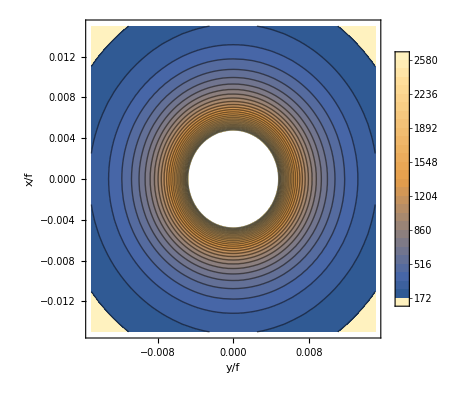
-Graphics- | -Graphics-

Intensity after lens

-Graphics- | -Graphics-

```mathematica
Clear["Global`*"]
x0=0;
y0=0;
z0=-0.001;
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=2f; (*plot half width value*)
xmaxAfter=3f;(*plot half width value*)
zmaxAfter=12f;(*plot full width value*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];

EσAfterLens=((√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped+ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};(*ρ,ϕ*)
EσAfterLensStar=((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};;
intensityAfterLens=EσAfterLens.EσAfterLensStar;
"Intensity before lens"
Grid[{{Evaluate[ContourPlot[intensityBeforeLens/.{r->√(x^2+y^2)+0,ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityBeforeLens/.{r->√(x^2+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√(x^2+z^2))]},{z,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
"Intensity after lens"
Grid[{{Evaluate[ContourPlot[intensityAfterLens/.{ρ->√(x^2+y^2),ϕ->ArcTan[x,y],z->0},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->All,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,zmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->All,Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
```

```mathematica
Clear["Global`*"]
x0=-0.001;
y0=0;
z0=0;
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=2f; (*plot half width value*)
xmaxAfter=3f;(*plot half width value*)
zmaxAfter=12f;(*plot full width value*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];

EσAfterLens=((√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped+ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};(*ρ,ϕ*)
EσAfterLensStar=((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};;
intensityAfterLens=EσAfterLens.EσAfterLensStar;
"Intensity before lens"
Grid[{{Evaluate[ContourPlot[intensityBeforeLens/.{r->√(x^2+y^2)+0,ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityBeforeLens/.{r->√(x^2+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√(x^2+z^2))]},{z,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
"Intensity after lens"
Grid[{{Evaluate[ContourPlot[intensityAfterLens/.{ρ->√(x^2+y^2),ϕ->ArcTan[x,y],z->0},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->All,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,zmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->All,Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
```

Intensity before lens

-Graphics- | -Graphics-

Intensity after lens

-Graphics- | -Graphics-

### Visualize intensity before/after lens with continuous contour plots (seems correct)

Scroll to the last cell to see a believable grid of atom displacements and corresponding emission patterns after the lens

```mathematica
Clear["Global`*"]
x0=-0.001;
y0=0;
z0=0;
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=2f; (*plot half width value*)
xmaxAfter=3f;(*plot half width value*)
zmaxAfter=12f;(*plot full width value*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];

EσAfterLens=((√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped+ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};(*ρ,ϕ*)
EσAfterLensStar=((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};
plotrange={100,10000};
intensityAfterLens=EσAfterLens.EσAfterLensStar;
(*Grid[{{ContourPlot[intensityBeforeLens/.{r->√(x^2+y^2)+0,ϕ->ArcTan[x,y],θ->ArcCos[0/(√(x^2+y^2+0))]},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->Automatic,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[intensityAfterLens/.{ρ->√(x^2+y^2),ϕ->ArcTan[x,y],z->0},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->All,Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]],}}]*)
"XZ slice"
Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->plotrange,Contours->30,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12]],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->plotrange,Contours->30,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12]],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}}]
```

XZ slice

-Graphics-

```mathematica
ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->plotrange,Contours->30,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12]]
```

-Graphics-

```mathematica
plotrange={0,20000};
contours=30;
pl=Legended[Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}}],BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]
```

-Graphics-

```mathematica
plotrange={0,20000};
contours=30;
pl=Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}}];Legended[pl,BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]
```

-Graphics-

```mathematica
Legended[Grid[{{pl,pl},{pl,pl}}],BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
xu=Array[1&,{2,2}]
```

{{1,1},{1,1}}

```mathematica
xu[[1,1]]=2
```

2

```mathematica
xu
```

{{2,1},{1,1}}

```mathematica
Clear["Global`*"];
x0Table ={-0.001,0,0.001};
z0Table ={-0.001,0,0.001};
plotArray=Array[1&,{Length[x0Table],Length[z0Table]}];
For[i=1,i<Length[x0Table]+1,i++,
For[j=1,j<Length[z0Table]+1,j++,
x0=x0Table[[i]];
y0=0;
z0=z0Table[[j]];
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=2f; (*plot half width value*)
xmaxAfter=3f;(*plot half width value*)
zmaxAfter=12f;(*plot full width value*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];

EσAfterLens=((√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped+ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};(*ρ,ϕ*)
EσAfterLensStar=((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};
intensityAfterLens=EσAfterLens.EσAfterLensStar;

plotrange={0,20000};
contours=30;
pl=Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}},PlotLabel->ToString[StringForm["x0=``, z0=``",x0,z0]]];
plotArray[[i,j]]=pl
(*Legended[pl,BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]*)
];
];
```

```mathematica
Legended[Grid[plotArray],BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Verify that this plot, for x0=y0=z0=0, gives the same result as one with original expressions. Note that I have inserted the factors of √2 in front of my generalized expressions, as they appear in the original ones.

```mathematica
Clear["Global`*"];
x0=y0=z0=0;
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
xmaxBefore=2f; (*plot half width value*)
xmaxAfter=3f;(*plot half width value*)
zmaxAfter=12f;(*plot full width value*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;
EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
θθHatMapped=(θθHat.θHat)ρHat+(θθHat.ϕHat)ϕHat+(θθHat.rHat)zHat;
ϕϕHatMapped=(ϕϕHat.θHat)ρHat+(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.rHat)zHat;
Clear[rr];

EσAfterLens=√2((√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped+ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};(*ρ,ϕ*)
EσAfterLensStar=√2((√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHatMapped-ⅈ ϕϕHatMapped)√Cos[θ])/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};
intensityAfterLens=EσAfterLens.EσAfterLensStar;

plotrange={0,20000};
contours=30;
Legended[Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}},PlotLabel->ToString[StringForm["x0=``, z0=``",x0,z0]]],BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]

EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k r+ϕ)))/r{Cos[θ],ⅈ};(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k r+ϕ)))/r{Cos[θ],-ⅈ};
intensityBeforeLens=EσBeforeLens.EσBeforeLensStar;
Eσ= √2 √(3/(16π))(ⅈ ⅇ^(ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),ⅈ};
EσStar=√2 √(3/(16π))(-ⅈ ⅇ^(-ⅈ ϕ)f^(1/2))/((f^2+ρ^2)^(3/4)){(f/(√(f^2+ρ^2))),-ⅈ};
intensityAfterLens=EσStar.Eσ;
Legended[Show[ContourPlot[intensityBeforeLens/.{r->√(x^2+(z+f)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z+f)/(√(x^2+(z+f)^2))]},{z,-2f,0},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],ContourPlot[intensityAfterLens/.{ρ->√(x^2+0),ϕ->ArcTan[x,0]},{z,0,2f},{x,-xmaxAfter,xmaxAfter},PlotRange->plotrange,Contours->contours,FrameLabel->{"z","x"},LabelStyle->Directive[Black, FontSize->12],ColorFunction->(ColorData["TemperatureMap",Rescale[#,plotrange]]&),ColorFunctionScaling->False],PlotRange->{{-2f,2f},{-xmaxAfter,xmaxAfter}},PlotLabel->"original expressions"],BarLegend[{"TemperatureMap",plotrange},Range[plotrange[[1]],plotrange[[-1]],10]]]
```

-Graphics-

-Graphics-

These results agree, but my integrands in the finite temperature cells toward the beginning of the notebook do not. So it may be that there is an error in the phase, which effectively cancels out when I compute the intensity for these plots. Todo...

### check lens transformation with a Gaussian beam (z dependence after lens not accounted for)

The output is, again, clearly missing z dependence after the lens, which has to be added “by hand”.

```mathematica
Clear["Global`*"]
x0=0;
y0=0;
z0=0;
f=5*^-3;
λ=7.8*^-7;
k=2π /λ;
w0=3*^-3;
zR=(π w0^2)/λ;
xmaxBefore=2w0/f; (*plot half width value, units f*)
xmaxAfter=2w0/f;(*plot half width value, units f*)
zmaxAfter=12;(*plot full width value, units f*)

rr=√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2);
ϕϕ=ArcTan[r Cos[ϕ]Sin[θ]-x0,r Sin[ϕ]Sin[θ]-y0];
θθ=ArcCos[(r Cos[θ]-z0)/(√((r Cos[ϕ]Sin[θ]-x0)^2+(r Sin[ϕ] Sin[θ]-y0)^2+(r Cos[θ]-z0)^2))];
(*rrHat={Cos[ϕϕ]Sin[θθ], Sin[ϕϕ]Sin[θθ], Cos[θθ]};*)
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
(*ϕϕHat={-Sin[ϕϕ],Cos[ϕϕ],0};*)
ϕHat={-Sin[ϕ],Cos[ϕ],0};
(*θθHat={Cos[ϕϕ]Cos[θθ],Sin[ϕϕ]Cos[θθ],-Sin[θθ]};*)
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
ρHat={Cos[ϕ],Sin[ϕ],0};
zHat={0,0,1};
xHat={1,0,0};
(*ϕϕHatDecomp=(ϕϕHat.ϕHat)ϕHat+(ϕϕHat.θHat)θHat+(ϕϕHat.rHat)rHat;
θθHatDecomp=(θθHat.ϕHat)ϕHat+(θθHat.θHat)θHat+(θθHat.rHat)rHat;
rrHatDecomp=(rrHat.ϕHat)ϕHat+(rrHat.θHat)θHat+(rrHat.rHat)rHat;*)
(*EσBeforeLens=√(3/(16π))(ⅈ ⅇ^(ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat+ⅈ ϕϕHat);(*θ,ϕ*)
EσBeforeLensStar=√(3/(16π))(-ⅈ ⅇ^(-ⅈ (k rr+ϕϕ)))/rr(Cos[θθ]θθHat-ⅈ ϕϕHat);*)
intensityBeforeLens=1/(1+((r Cos[θ])/zR)^2)Exp[(-2(r Sin[θ])^2)/w0^2];(*EσBeforeLens.EσBeforeLensStar*);
(*intensityAfterLens=(Cos[θ]/(1+((r Cos[θ])/zR)^2)Exp[(-2(r Sin[θ])^2)/w0^2]/.rr->(√((ρ+((θθHat.rHat)/(θθHat.θHat))(z-f))^2+(f-z0)^2)))/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};*)
xHat={1,0,0};
xHatMapped=(xHat.θHat)ρHat+(xHat.ϕHat)ϕHat+(xHat.rHat)zHat;
intensityAfterLens=(Cos[θ]^2/(1+((r Cos[θ])/zR)^2)Exp[(-2(r Sin[θ])^2)/w0^2]xHatMapped.xHatMapped)/.{r->√(ρ^2+f^2),θ->ArcCos[f/(√(f^2+ρ^2))]};
"Intensity before lens"
Grid[{{Evaluate[ContourPlot[intensityBeforeLens/.{r->√((x f)^2+(y f)^2+0),ϕ->ArcTan[x,y],θ->ArcCos[0/(√((x f)^2+(y f)^2+0))]},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->{0,1},Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityBeforeLens/.{r->√((x f)^2+(z f)^2),ϕ->ArcTan[x f,0 f],θ->ArcCos[(z f)/(√((x f)^2+(z f)^2))]},{z,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->{0,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
"Intensity after lens"
Grid[{{Evaluate[ContourPlot[intensityAfterLens/.{ρ->√((x f)^2+(y f)^2),ϕ->ArcTan[x,y],z->0},{y,-xmaxAfter,xmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->{0,1},Contours->30,FrameLabel->{"y/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]],ContourPlot[intensityAfterLens/.{ρ->√((x f)^2+0),ϕ->ArcTan[f x,0]},{z,0,zmaxAfter},{x,-xmaxAfter,xmaxAfter},PlotLegends->Automatic,PlotRange->{0,1},Contours->30,FrameLabel->{"z/f","x/f"},LabelStyle->Directive[Black, FontSize->12]]}}]
```

Intensity before lens

-Graphics- | -Graphics-

Intensity after lens

-Graphics- | -Graphics-

```mathematica
xHatMapped
```

{Cos[θ] Cos[ϕ]^2+Sin[ϕ]^2,-Cos[ϕ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ϕ],Cos[ϕ] Sin[θ]}

```mathematica
xHatMapped
```

{Cos[θ] Cos[ϕ]^2+Sin[ϕ]^2,-Cos[ϕ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ϕ],Cos[ϕ] Sin[θ]}

```mathematica
Clear[w0,zR,f]
intensityAfterLens
```

(0.005 ⅇ^(-2000000/9 (1/40000+ρ^2) (1-1/(40000 (1/40000+ρ^2)))) ((1-1/(40000 (1/40000+ρ^2))) Cos[ϕ]^2+(-Cos[ϕ] Sin[ϕ]+(Cos[ϕ] Sin[ϕ])/(200 √(1/40000+ρ^2)))^2+(Cos[ϕ]^2/(200 √(1/40000+ρ^2))+Sin[ϕ]^2)^2))/(√(1/40000+ρ^2))

```mathematica
intensityAfterLens/.{ρ->√((x f)^2+0),ϕ->ArcTan[f x,0]}
```

1. ⅇ^(-1000000/9 (1/40000+x^2/40000) (1-1/(40000 (1/40000+x^2/40000))));;Intensity before lens

```mathematica
ContourPlot[1/(1+(z/zR)^2)Exp[(-2 x^2)/w0^2],{z,-2zR,2zR},{x,-2 w0,2w0},Contours->30,PlotRange->All]
```

-Graphics-

### Plotting field components (probably not correct)

```mathematica
VectorPlot[{1/(√(x+y))ⅇ^(ⅈ √(x+y)),1/(√(x+y))ⅇ^(ⅈ √(x+y))},{x,0,5},{y,0,5}]
```

VectorPlot[{ⅇ^(ⅈ √(x+y))/(√(x+y)),ⅇ^(ⅈ √(x+y))/(√(x+y))},{x,0,5},{y,0,5}]

```mathematica
(*this almost looks correct, except that, conspicuously, there is symmetry about the xz and xy axes where there should not be. the xy plot doesn't circulate as it should*)
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
Ex=Abs[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[1]]];
Ey=Abs[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[2]]];
Ez=Abs[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[3]]];
Grid[{{VectorPlot[{Ex,Ey}/.{r->√(x^2+y^2),ϕ->ArcTan[x,y],θ->ArcCos[0.001/(√((x )^2+(y )^2+10^-6))]},{x,-1,1},{y,-1,1}],
VectorPlot[{Ez,Ex}/.{r->√(x^2+z^2),ϕ->ArcTan[x,0],θ->ArcCos[z/(√((x )^2+(z )^2))]},{z,-1,1},{x,-1,1}]}}]
```

-Graphics- | -Graphics-

```mathematica
(*this almost looks correct, except that, conspicuously, there is symmetry about the xz and xy axes where there should not be. the xy plot doesn't circulate as it should*)
rHat={Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]};
ϕHat={-Sin[ϕ],Cos[ϕ],0};
θHat={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],-Sin[θ]};
λ=7.8*^-7;
k=2π/λ;
xmax=0.1;(*half-width of the plots in units λ*)
yoffset=0.1λ;
(*Ex=Re[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[1]]];
Ey=Re[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[2]]];
Ez=Re[(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[3]]];*)
Ex=(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[1]];
Ey=(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[2]];
Ez=(ⅇ^(ⅈ(k r+ϕ))/r(Cos[θ]θHat +ⅈ ϕHat))[[3]];
Grid[{{VectorPlot[Abs[{Ex,Ey}/.{r->√((x λ)^2+(y λ)^2),ϕ->ArcTan[x,y],θ->ArcCos[yoffset/(√((x λ)^2+(y λ )^2+yoffset^2))]}],{x,-xmax,xmax},{y,-xmax,xmax}],
VectorPlot[Re[{Ez,Ex}/.{r->√((λ x)^2+(z λ)^2),ϕ->ArcTan[x,0],θ->ArcCos[(z λ)/(√((x λ)^2+(z λ)^2))]}],{z,-xmax,xmax},{x,-xmax,xmax}]}}]
```

-Graphics- | -Graphics-

```mathematica
Ex
```

Real[(ⅇ^(ⅈ (8.05537×10^6 r+ϕ)) (Cos[θ]^2 Cos[ϕ]-ⅈ Sin[ϕ]))/r]

```mathematica
Random variate for atom positions in a 3D
```

```mathematica
Random variate for atom positions in a 3D
```